```mathematica
<< "/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
projectHomeDir="./";
lineThickness=0.012;
legendThickness=lineThickness*20;
labelSize=22;
tickSize=17;
legendSize=19;
textSize=22;
(*colours=ColorData[97,"ColorList"];*)
(*Coulour-blind frendly colour set *)
colours={RGBColor["#56B4E9"],RGBColor["#009E73"],RGBColor["#F0E442"],RGBColor["#0072B2"],RGBColor["#D55E00"],RGBColor["#CC79A7"],RGBColor["#999999"],RGBColor["#E69F00"]};
(*colours={RGBColor["#e41a1c"],RGBColor["#377eb8"],RGBColor["#4daf4a"],RGBColor["#984ea3"],RGBColor["#ff7f00"],RGBColor["#ffff33"]};*)
colours={RGBColor["#000000"],RGBColor["#3DB7E9"],RGBColor["#F748A5"],RGBColor["#359B73"],RGBColor["#e69f00"],RGBColor["#2271B2"],RGBColor["#f0e442"],RGBColor["#d55e00"]}
```

{RGBColor[0., 0., 0.],RGBColor[0.23921568627450981, 0.7176470588235294, 0.9137254901960784],RGBColor[0.9686274509803922, 0.2823529411764706, 0.6470588235294118],RGBColor[0.20784313725490197, 0.6078431372549019, 0.45098039215686275],RGBColor[0.9019607843137255, 0.6235294117647059, 0.],RGBColor[0.13333333333333333, 0.44313725490196076, 0.6980392156862745],RGBColor[0.9411764705882353, 0.8941176470588236, 0.25882352941176473],RGBColor[0.8352941176470589, 0.3686274509803922, 0.]}

```mathematica
sol3disapcheck= Solve[((-974143752064000 qb^3+5012853613824000 n qb^3-10688982648960000 n^2 qb^3+12087790650880000 n^3 qb^3-7645855916160000 n^4 qb^3+2564864918784000 n^5 qb^3-356526866304000 n^6 qb^3-935178001981440000 qb^4-50471292604113024000 n qb^4+219055881267538560000 n^2 qb^4-366513243560962176000 n^3 qb^4+302501996075303808000 n^4 qb^4-123746664499008768000 n^5 qb^4+20108197858775040000 n^6 qb^4-285639892195834176000 qb^5-16348654502077720704000 n qb^5+86599788173872632960000 n^2 qb^5-165667882605990481920000 n^3 qb^5+151709125485203244672000 n^4 qb^5-67821486074351455488000 n^5 qb^5+11951186648686411392000 n^6 qb^5-27596128694720230400000 qb^6+89340939141486305280000 n qb^6+41633284651585589760000 n^2 qb^6-355722850352023526400000 n^3 qb^6+270978086574111436800000 n^4 qb^6+30662030649168414720000 n^5 qb^6-54988664936330567680000 n^6 qb^6-8425134055885412544000 qb^7-24520609773747620736000 n qb^7+460257815265707598720000 n^2 qb^7-1333614470342453483520000 n^3 qb^7+1369765000034825186688000 n^4 qb^7-560110965332770182912000 n^5 qb^7+271251094176170656128000 n^6 qb^7+50766780772438832640000 qb^8-328089559277694592896000 n qb^8+1076974936405970797440000 n^2 qb^8-2470270863759217728384000 n^3 qb^8+3298096287440028396672000 n^4 qb^8-1495802484519385658112000 n^5 qb^8-420364546273810575360000 n^6 qb^8+21614341510689866624000 qb^9-194298315501788623104000 n qb^9+711658784395007352960000 n^2 qb^9-1357323216421249441280000 n^3 qb^9+1420784975251242437760000 n^4 qb^9-774429910373962047744000 n^5 qb^9+171993341140060454784000 n^6 qb^9)^2+4 (-78400 (562 qb-964 n qb+405 n^2 qb+179840 qb^2-467526 n qb^2+221926 n^2 qb^2+78961 qb^3-472642 n qb^3+628881 n^2 qb^3)^2+235200 (281 qb^2-482 n qb^2+204 n^2 qb^2-562 n qb^3+1402 n^2 qb^3) (281-482 n+202 n^2+179840 qb+1331436 n qb-1065876 n^2 qb+28403761 qb^2-86959522 n qb^2+62095802 n^2 qb^2+22109080 qb^3-88278960 n qb^3+88121880 n^2 qb^3))^3)==0,n];
```

```mathematica
bifPintCInoiseViaUAsymc=FullSimplify[sol3disapcheck⟦9⟧⟦1,2⟧]
```

1/4 (((3+qb) (1+3 qb))/(-1+qb)^2-√(((3+qb)^2 (1+3 qb)^2-8 (-1+qb^2)^2+6 2^(1/3) (-1+qb)^2 (-qb (-1+qb^2)^2)^(1/3))/(-1+qb)^4)-√2 √((-8 (-1+qb)^4 (1+qb)^2+(-1+qb)^2 (3+qb)^2 (1+3 qb)^2-3 2^(1/3) (-1+qb)^4 (-qb (-1+qb^2)^2)^(1/3)+((1+qb (6+qb)) (1+qb (-132+qb (-250+(-132+qb) qb))))/(√(1+256/(-1+qb)^4+512/(-1+qb)^3+320/(-1+qb)^2+64/(-1+qb)+(6 2^(1/3) (-qb (-1+qb^2)^2)^(1/3))/(-1+qb)^2)))/(-1+qb)^6))

0.999

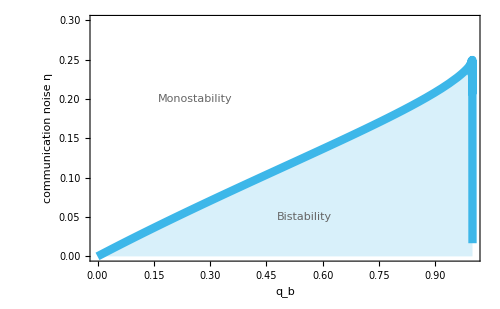

```mathematica
maxQ=0.999
plt=Show[Plot[Re[bifPintCInoiseViaUAsymc],{qb,0,maxQ},PlotRange->Full,
PlotStyle->Directive[{colours[[2]],Thickness[lineThickness]}],Filling->0
],
Graphics[{Style[Text["Monostability",{0.26,0.20}],Directive[{textSize,GrayLevel[0.4]}]],Style[Text["Bistability",{0.55,0.05}],Directive[{textSize,GrayLevel[0.4]}]]
}],PlotRange->{{0,maxQ},{0,0.3}},Axes->False,FrameStyle->Directive[{Thickness[.005]}],
PlotRangePadding->0,
ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"q_b","communication noise η"}]
```

```mathematica
Export["/Volumes/My_Passport/argosim2/Runs/acc/images/ODE-CI-bifurc-zq.pdf",plt]
```

/Volumes/My_Passport/argosim2/Runs/acc/images/ODE-CI-bifurc-zq.pdf